# Quantum estimation of a Schmidt parameter

Dr Jesús Rubio
School of Mathematics and Physics, University of Surrey
j.rubiojimenez@surrey.ac.uk
ORCID iD: 0000-0002-8193-8273

Application of the results in:

	J. Rubio, First-principles construction of symmetry-informed quantum metrologies, arXiv:2402.16410 (2024)
	
Created: December 2023
Last updated: May 2024

## Prior information

### Prior knowledge

Values for the numerical example:

```mathematica
Clear[ a,θmin,θmax]
a=0.01;θmin=a;θmax=1-a;
```

Symmetry function:

```mathematica
Clear[f,finv]
f[θ_]=2ArcTanh[2θ-1]; finv[θ_]=1/2+Tanh[θ/2]/2;
```

### Prior probability

```mathematica
Clear[p]
p = 1/(θ(1-θ));p= p/Integrate[p,{θ,θmin,θmax}]
```

0.108811/((1-θ) θ)

### Prior uncertainty

```mathematica
Clear[ϵprior]
ϵprior = NIntegrate[p f[θ]^2,{θ,θmin,θmax}]-NIntegrate[p f[θ],{θ,θmin,θmax},AccuracyGoal->8]^2
```

7.03838

## State operators

### Probe state

Working in the Schmidt basis:

```mathematica
Clear[ψ,ρ]
ψ={Sqrt[θ],Sqrt[1-θ]};
ρ=KroneckerProduct[ConjugateTranspose[ψ],ψ];
ρ//MatrixForm
```

(θ | √(1-θ) √θ
√(1-θ) √θ | 1-θ)

### ρ_0, ρ_1 and ρ_2 operators

```mathematica
Clear[ρ0,ρ1,ρ2]
ρ0=NIntegrate[p ρ,{θ,θmin,θmax}];
ρ1=Chop[NIntegrate[p ρ f[θ],{θ,θmin,θmax},AccuracyGoal->8]];
ρ2=NIntegrate[p ρ f[θ]^2,{θ,θmin,θmax}];
Row[{MatrixForm[ρ0],", ",MatrixForm[ρ1],", ",MatrixForm[ρ2]}]
```

(0.5 | 0.298243
0.298243 | 0.5), (0.982036 | 0
0 | -0.982036), (3.51919 | 1.30031
1.30031 | 3.51919)

## Optimal measurement

### S operator

```mathematica
Clear[S]
S=Chop[LyapunovSolve[ρ0,2ρ1]];S//MatrixForm
```

(1.96407 | 0
0 | -1.96407)

### POM

```mathematica
Clear[s1ket,s2ket,optPOM1,optPOM2]
{s1ket,s2ket}=Map[Normalize,Eigenvectors[S]]; 
optPOM1=KroneckerProduct[s1ket,s1ket];optPOM2=KroneckerProduct[s2ket,s2ket];
Row[{MatrixForm[optPOM1],", ",MatrixForm[optPOM2]}]
```

(0. | 0.
0. | 1.), (1. | 0.
0. | 0.)

## Local measurement, version A

### SLD

```mathematica
Clear[ℒ] 
ℒ=2D[ρ,θ];ℒ//MatrixForm//FullSimplify
```

(2 | (1-2 θ)/(√(-((-1+θ) θ)))
(1-2 θ)/(√(-((-1+θ) θ))) | -2)

### POM

```mathematica
Clear[l1ketA,l2ketA,locPOM1A,locPOM2A] 
l1ketA={1-2θ,1-2Sqrt[θ(1-θ)]}/Sqrt[2-4Sqrt[θ(1-θ)]];l2ketA={1-2θ,-1-2Sqrt[θ(1-θ)]}/Sqrt[2+4Sqrt[θ(1-θ)]];
locPOM1A[θ_]=KroneckerProduct[l1ketA,l1ketA];locPOM2A[θ_]=KroneckerProduct[l2ketA,l2ketA];
Row[{MatrixForm[l1ketA],", ",MatrixForm[l2ketA]}]
```

((1-2 θ)/(√(2-4 √((1-θ) θ)))
(1-2 √((1-θ) θ))/(√(2-4 √((1-θ) θ)))), ((1-2 θ)/(√(2+4 √((1-θ) θ)))
(-1-2 √((1-θ) θ))/(√(2+4 √((1-θ) θ))))

Checks:

```mathematica
{l1ketA.l1ketA,l2ketA.l2ketA,l1ketA.l2ketA}//FullSimplify
```

{1,1,0}

```mathematica
Row[{MatrixForm[ℒ.l1ketA-l1ketA/Sqrt[θ(1-θ)]],", ",MatrixForm[ℒ.l2ketA+l2ketA/Sqrt[θ(1-θ)]]}]//FullSimplify
```

(0
0), (0
0)

### Estimator

```mathematica
Clear[θl1A,θl2A]
θl1A[x_]:=finv[NIntegrate[p Tr[locPOM1A[x].ρ]f[θ],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM1A[x].ρ],{θ,θmin,θmax}]]
θl2A[x_]:=finv[NIntegrate[p Tr[locPOM2A[x].ρ]f[θ],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM2A[x].ρ],{θ,θmin,θmax}]]
```

## Local measurement, version B

Projecting onto the initial state:

### POM

```mathematica
Clear[l1ketB,l2ketB,locPOM1B,locPOM2B] 
l1ketB=ψ;l2ketB={ψ[[2]],-ψ[[1]]};
locPOM1B[θ_]=KroneckerProduct[l1ketB,l1ketB];locPOM2B[θ_]=KroneckerProduct[l2ketB,l2ketB];
Row[{MatrixForm[l1ketB],", ",MatrixForm[l2ketB]}]
```

(√θ
√(1-θ)), (√(1-θ)
-√θ)

A check:

```mathematica
{l1ketB.l1ketB,l2ketB.l2ketB,l1ketB.l2ketB}//FullSimplify
```

{1,1,0}

### Estimator

```mathematica
Clear[θl1B,θl2B]
θl1B[x_]:=finv[NIntegrate[p Tr[locPOM1B[x].ρ]f[θ],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM1B[x].ρ],{θ,θmin,θmax}]]
θl2B[x_]:=finv[NIntegrate[p Tr[locPOM2B[x].ρ]f[θ],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM2B[x].ρ],{θ,θmin,θmax}]]
```

## Performance

### Mean hyperbolic error

```mathematica
Clear[ϵMHE]
ϵMHE=Tr[ρ2-S.ρ1]
```

3.1808

```mathematica
Clear[ϵlocMHEa,ϵlocMHEb]
ϵlocMHEa[x_]:= Tr[ρ2]-NIntegrate[p (Tr[locPOM1A[x].ρ]f[θl1A[x]]^2+Tr[locPOM2A[x].ρ]f[θl2A[x]]^2),{θ,θmin,θmax}]
ϵlocMHEb[x_]:= Tr[ρ2]-NIntegrate[p (Tr[locPOM1B[x].ρ]f[θl1B[x]]^2+Tr[locPOM2B[x].ρ]f[θl2B[x]]^2),{θ,θmin,θmax}]
```

### Plot

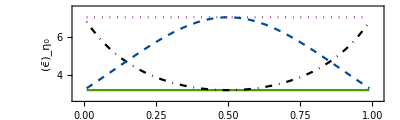

```mathematica
Plot[{ϵMHE,ϵlocMHEa[y],ϵlocMHEb[y],ϵprior},{y,θmin,θmax},
PlotRange->{{θmin-0.03,θmax+0.03},{ϵMHE-0.5,ϵprior+0.5}},
PlotStyle->{{RGBColor[0.3,0.6,0]},{DotDashed,Black},{Dashed,RGBColor[0,0.3,0.6]},{Dotted,Purple}},
Frame->True,FrameLabel->{"η_0","(ϵ̄)_η_0"},FrameStyle->Directive["Times",12,Black],AspectRatio->0.3]
```